```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/nightmareforev/git/root_tracking/Mathematica/SRSPM/Singularity_event

## Required libraries and functions:

```mathematica
SetDirectory[NotebookDirectory[]];
<<"rotationtools.wl"
<<"kinematic_utils.m"
```

```mathematica
(*Run the following commands if MaTeX is not already installed and configured with Mathematica in your PC*)
```

```mathematica
(*ResourceFunction["MaTeXInstall"][]*)
```

```mathematica
(*ConfigureMaTeX[
"pdfLaTeX"->"/usr/bin/pdflatex"
]*)
```

```mathematica
<<MaTeX`
```

```mathematica
T[x_]:=Transpose[x];
mf[x_]:=MatrixForm[x];
dim[x_]:=Dimensions[x];
```

## Architecture of the SRSPM:

```mathematica
(*Assuming all the legs are made of steel*)
```

```mathematica
(*Similar set of data for 6-RSS has shown that these values are too high*)
```

```mathematica
leglparam = {ro->0.04/2, ri->0.035/2, ρ-> 7858, lb->0.7, la->1.2};
legmparam = {ma->ρ*π*ri^2*la, mb-> ρ*π*(ro^2-ri^2)*lb, g->9.8}/.leglparam;
ibzi =  mb*(ri^2+ro^2)/2;
ibxi = mb*(3*(ro^2+ri^2)+lb^2)/12;
ibyi = mb*(3*(ro^2+ri^2)+lb^2)/12;

iazi =  ma*ri^2/2;
iaxi = ma*(3*ri^2+la^2)/12;
iayi = ma*(3*ri^2+la^2)/12;

(*Mass and inertial values are from the CAD model*)
datap ={rb->1, rt->0.5803, γt->0.6573, γb->0.2985};
tplparam = {ρ->2810, t->0.01}/.datap;
(*tpmparam = mtp-> ρ*t*3*√3/2*rt^2/.tplparam/.datap;*)
tpmparam = mtp-> 0.20339;
(*itpz = mtp*rt^2*(1-(2/3)*Sin[π/6]^2);
itpx = itpz/2;
itpy = itpz/2;*)
itpz = 2.343101;
itpx = 1.17172;
itpy =  1.17172;

(*Assuming manipulator is symmetric in construction*)
Ibi = {{ibxi, 0, 0}, {0,ibyi, 0}, {0, 0,ibzi}};
Iai ={{iaxi,0,0}, {0,iayi,0},{0,0,iazi}};
Itp = {{itpx, 0, 0}, {0, itpy, 0}, {0, 0, itpz}};
```

```mathematica
b1 = {rb, 0, 0};
b2 = rotZ[2*γb].b1;
b3 = rotZ[2π/3].b1;
b4 = rotZ[2π/3].b2;
b5 = rotZ[4π/3].b1;
b6 = rotZ[4π/3].b2;
```

```mathematica
b = Table[Symbol["b"<>ToString[i]],{i, 6}];
```

```mathematica
(b)[[2]]
```

{rb Cos[2 γb],rb Sin[2 γb],0}

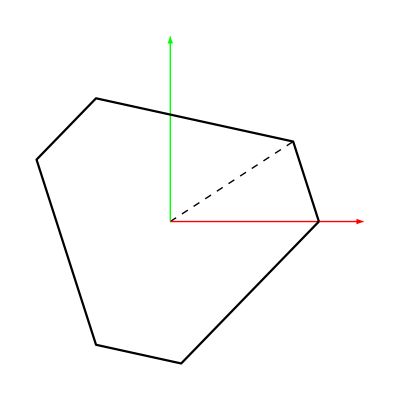

```mathematica
Show[Graphics[{Dashed, Line[{{0,0}, (b/.datap)[[2]][[1;;2]]}]}], Graphics[{Green, Arrow[{{0,0},{0,1.3}}]}],Graphics[{Red, Arrow[{{0,0},{1.3,0}}]}], ListLinePlot[Join[(b/.datap), {(b/.datap)[[1]]}][[;;, 1;;2]], PlotStyle->Black], AspectRatio->1, ImageResolution->600]
```

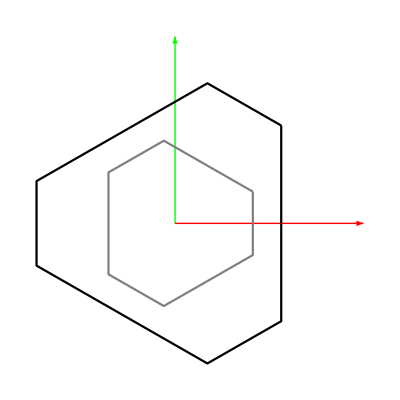

```mathematica
(*Assuming that the center of the global axis is in the center of the bottom plate and hence all the ground joints are denoted by bi and the top plate edges by ai*)
(*Locations of all the known ground joints*)
b1 = {rb, 0, 0};
b2 = rotZ[2*γb].b1;
b3 = rotZ[2π/3].b1;
b4 = rotZ[2π/3].b2;
b5 = rotZ[4π/3].b1;
b6 = rotZ[4π/3].b2;

tempb = Table[Symbol["b"<>ToString[i]],{i, 6}];

b = Table[rotZ[(2π/3-2*γb)/2].tempb[[i]],{i, Length[tempb]}];

al1 = {rt, 0, 0};
al2 = rotZ[2*γt].al1;
al3 = rotZ[2π/3].al1;
al4 = rotZ[2π/3].al2;
al5 = rotZ[4π/3].al1;
al6 = rotZ[4π/3].al2;
tempal = Table[Symbol["al"<>ToString[i]],{i, 6}];
al = Table[rotZ[(2π/3-2γt)/2].tempal[[i]],{i, Length[tempal]}];
Show[Graphics[{Green, Arrow[{{0,0},{0,1.3}}]}],Graphics[{Red, Arrow[{{0,0},{1.3,0}}]}], ListLinePlot[Join[(b/.datap), {(b/.datap)[[1]]}][[;;, 1;;2]], PlotStyle->Black],ListLinePlot[Join[(al/.datap), {(al/.datap)[[1]]}][[;;, 1;;2]],PlotStyle->Gray], AspectRatio->1, ImageResolution->600]
```

```mathematica
b/.datap
```

{{0.732576,0.680685,0},{0.223203,0.974772,0},{-0.955779,0.294087,0},{-0.955779,-0.294087,0},{0.223203,-0.974772,0},{0.732576,-0.680685,0}}

```mathematica
cords = {"x", "y", "z"};
```

```mathematica
acords = Table[Table[Symbol["a"<>ToString[j]<>cords[[i]]],{i, 3}],{j, 6}]
```

{{a1x,a1y,a1z},{a2x,a2y,a2z},{a3x,a3y,a3z},{a4x,a4y,a4z},{a5x,a5y,a5z},{a6x,a6y,a6z}}

```mathematica
Inner[Rule, Flatten[acords], Flatten[b/.datap], List]
```

{a1x→0.732576,a1y→0.680685,a1z→0,a2x→0.223203,a2y→0.974772,a2z→0,a3x→-0.955779,a3y→0.294087,a3z→0,a4x→-0.955779,a4y→-0.294087,a4z→0,a5x→0.223203,a5y→-0.974772,a5z→0,a6x→0.732576,a6y→-0.680685,a6z→0}

## Inverse Kinematics:

```mathematica
(*Assuming that the center of the global axis is in the center of the bottom plate and hence all the ground joints are denoted by bi and the top plate edges by ai*)
l= Table[Symbol["l"<>ToString[i]],{i, 6}];
(*a = Table[Symbol["a"<>ToString[i]],{i, 6}];*)
ϕ = Table[Symbol["ϕ"<>ToString[i]],{i,6}];
ψ = Table[Symbol["ψ"<>ToString[i]],{i,6}];
```

```mathematica
(*Considering ϕi, ψi and li's as the configuration space q*)
(*Rotation matrix of any leg li*)
Rl = Table[rotY[ϕ[[i]]].rotX[ψ[[i]]],{i, 6}];
(*Angular velocity Jacobian of each leg*)
Jωl = Table[SkewMat2vec[Simplify[T[Rl[[i]]].D[Rl[[i]],{Join[ϕ,ψ, l]}]]],{i, 6}];
(*a in global frame via b*)
a  = Table[b[[i]]+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, l[[i]]},{i, 6}];
```

```mathematica
(*The mid point of the top platform will be*)
ptp = Total[a]/6;
```

```mathematica
(*(*Now consider the three points a1, a5, a6 so that the local orientation of the top platform is along the global frame*)
a65 = Simplify[((a[[6]]-a[[5]])/Sqrt[((b[[6]]-b[[5]]).(b[[6]]-b[[5]]))/.rb->rt/.γb->γt])];
a15 = Simplify[((a[[1]]-a[[5]])/Sqrt[((b[[1]]-b[[5]]).(b[[1]]-b[[5]]))/.rb->rt/.γb->γt])];
(*a12 and a13 are unit vectors, but the cross need not be a unit vector and hence the Rotation matrix columns need to be re-normalised*)
(*We need to find the magnitude of the second and the third axes*)*)
```

```mathematica
(*Now consider the three points a1, a5, a6 so that the local orientation of the top platform is along the global frame*)
a56 = Simplify[((a[[5]]-a[[6]])/Sqrt[((b[[5]]-b[[6]]).(b[[5]]-b[[6]]))/.rb->rt/.γb->γt])];
a16 = Simplify[((a[[1]]-a[[6]])/Sqrt[((b[[1]]-b[[6]]).(b[[1]]-b[[6]]))/.rb->rt/.γb->γt])];
```

```mathematica
(*sinangle = Simplify[(Cross[(b[[6]]-b[[5]])/Sqrt[(b[[6]]-b[[5]]).(b[[6]]-b[[5]])], (b[[1]]-b[[5]])/Sqrt[(b[[1]]-b[[5]]).(b[[1]]-b[[5]])]]/.rb->rt/.γb->γt)[[3]]];
zaxis = Simplify[Cross[a65, a15]/sinangle];
Rtp = {a65,  Cross[zaxis, a65], zaxis};*)
```

```mathematica
sinangle = Simplify[(Cross[(b[[1]]-b[[6]])/Sqrt[(b[[1]]-b[[6]]).(b[[1]]-b[[6]])], (b[[5]]-b[[6]])/Sqrt[(b[[5]]-b[[6]]).(b[[5]]-b[[6]])]]/.rb->rt/.γb->γt)[[3]]];
zaxis = Simplify[Cross[a16, a56]/sinangle];
Rtp = { Cross[a16, zaxis],a16, zaxis};
```

```mathematica
(*Now that we have obtained the rotation matrix, we can find the angular velocity Jacobian of the top plate*)
Jωt = SkewMat2vec[T[Rtp].D[Rtp,{Join[ϕ, ψ, l]}]];
```

```mathematica
(*CoM of the two parts of the prismatic joints*)
pa  = Table[b[[i]]+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, l[[i]]-la/2},{i, 6}];
pb  = Table[b[[i]]+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, lb/2},{i, 6}];
(*First case where ϕi, ψi and li's are given. Contains all the Jacobians*)
Jpai = D[pa, {Join[ϕ, ψ, l]}];
Jpbi = D[pb, {Join[ϕ, ψ, l]}];
Jtp = D[ptp,  {Join[ϕ, ψ, l]}];
```

```mathematica
(*To generate the test data for this system*)
tpdat = {c1->0, c2->0, c3->0, x->0, y->0, z->1.1};
```

```mathematica
qrule =Flatten[Table[{ϕ[[i]]-> ϕ[[i]][t], ψ[[i]]->ψ[[i]][t], l[[i]]->l[[i]][t]},{i, 6}]];
q = Join[ϕ, ψ, l]/.qrule;
```

```mathematica
Amat = vec2SkewMat[{c1, c2, c3}];
Rdat = Simplify[Inverse[(IdentityMatrix[3]-Amat)].(IdentityMatrix[3]+Amat)];
Simplify[Rdat.T[Rdat]]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
Rtps = Rtp/.qrule/.datap/.leglparam/.legmparam/.tpmparam/.tpdat;
aldat = al/.datap;
ag =Simplify[Table[{x, y, z}+Rdat.aldat[[i]],{i, 6}]]/.tpdat;
bdat = b/.datap;
```

```mathematica
(*Formulating the constraint equations*)
```

```mathematica
η1 = Join[Simplify[Expand[Table[(a[[i]]-a[[i+1]]).(a[[i]]-a[[i+1]])-(al[[i]]-al[[i+1]]).(al[[i]]-al[[i+1]]),{i, 5}]]], {Simplify[Expand[(a[[6]]-a[[1]]).(a[[6]]-a[[1]])-(al[[6]]-al[[1]]).(al[[6]]-al[[1]])]], Simplify[Expand[(a[[1]]-a[[3]]).(a[[1]]-a[[3]])-(al[[3]]-al[[1]]).(al[[3]]-al[[1]])]], Simplify[Expand[(a[[1]]-a[[4]]).(a[[1]]-a[[4]])-(al[[1]]-al[[4]]).(al[[1]]-al[[4]])]], Simplify[Expand[(a[[1]]-a[[5]]).(a[[1]]-a[[5]])-(al[[1]]-al[[5]]).(al[[1]]-al[[5]])]], Expand[(a[[1]]-a[[3]]).Cross[a[[1]]-a[[2]], a[[1]]-a[[4]]]], Expand[(a[[1]]-a[[4]]).Cross[a[[1]]-a[[3]], a[[1]]-a[[5]]]], Expand[(a[[1]]-a[[5]]).Cross[a[[1]]-a[[4]], a[[1]]-a[[6]]]]}];
```

```mathematica
ηconfig = η1/.datap/.leglparam/.legmparam/.tpmparam/.qrule;
```

```mathematica
(*Therefore the sample solution satisfies the constraint equations*)
```

```mathematica
(*ηconfig/.datap/.leglparam/.legmparam/.tpmparam/.sampledat/.qrule*)
```

```mathematica
p = Table[Symbol["p"<>ToString[i]],{i,6}]; (*p is tan ϕ/2*)
s = Table[Symbol["s"<>ToString[i]],{i,6}]; (*s is tan ψ/2*)
```

```mathematica
htanrule = Flatten[Table[{Cos[ϕ[[i]][t]]->(1-p[[i]]^2)/(1+p[[i]]^2),Sin[ϕ[[i]][t]]->(2*p[[i]])/(1+p[[i]]^2), Cos[ψ[[i]][t]]->(1-s[[i]]^2)/(1+s[[i]]^2),Sin[ψ[[i]][t]]->(2*s[[i]])/(1+s[[i]]^2) },{i,6}]];
```

```mathematica
(*iksolver module*)
```

```mathematica
als = {{al1x, al1y, 0}, {al2x, al2y, 0}, {al3x, al3y, 0}, {al4x, al4y, 0}, {al5x, al5y, 0}, {al6x, al6y, 0}};
bs = {{b1x, b1y, 0}, {b2x, b2y, 0}, {b3x, b3y, 0}, {b4x, b4y, 0}, {b5x, b5y, 0}, {b6x, b6y, 0}};
```

```mathematica
alsrules = Inner[Rule, Flatten[als[[;;, 1;;2]]], Flatten[al[[;;, 1;;2]]], List];
bsrules = Inner[Rule, Flatten[bs[[;;, 1;;2]]], Flatten[b[[;;, 1;;2]]], List];
```

```mathematica
atps = Table[pc+Rtp2.als[[i]],{i,6}];
ajs = Table[bs[[i]]+Rl[[i]].{0,0,l[[i]]},{i, 6}];
```

```mathematica
Arp = vec2SkewMat[{c1, c2, c3}];
Rtp2 = Simplify[Inverse[(IdentityMatrix[3]-Arp)].(IdentityMatrix[3]+Arp)];
pc = {x, y, z};
aj  = Table[b[[i]]+Rl[[i]].{0,0, l[[i]]},{i, Length[b]}];
atp = Table[pc+Rtp2.al[[i]],{i, Length[al]}];
```

```mathematica
(*Formulating constraints in the extended configuration space*)
```

```mathematica
ηext = Flatten[(aj-atp)]/.datap/.leglparam;
```

```mathematica
SetSystemOptions["SimplificationOptions"->"AutosimplifyTrigs"->False];
```

```mathematica
qx = {x, y, z, c1, c2, c3};
```

```mathematica
samplex = Inner[Rule, qx, {0,0,0.75,0,0,0}, List];
```

```mathematica
li2 = Table[(atp-bs)[[i]].(atp-bs)[[i]],{i, 6}];
li = Sqrt[Together[li2]];
lirule = Inner[Rule, l, li,List];
```

```mathematica
lval = Inner[Rule, l, Simplify[li/.alsrules/.bsrules/.datap], List];
clval = Compile[{{x, _Complex},{y, _Complex},{z, _Complex},{c1, _Complex},{c2, _Complex},{c3, _Complex}}, Evaluate[l/.lval]];
```

```mathematica
sinψ = Together[Table[Simplify[(atp[[i]][[2]]-Expand[aj[[i]][[2]]][[;;-2]])/(-l[[i]])], {i, 6}]];
cos2ψ = Table[((atp[[i]][[1]]-Expand[aj[[i]][[1]]][[;;-2]])/l[[i]])^2+(atp[[i]][[3]]/l[[i]])^2,{i, 6}];
cosψ = Sqrt[Together[cos2ψ]];
sinψrule = Inner[Rule, Table[Sin[ψ[[i]]],{i, 6}], sinψ, List];
cosψrule = Inner[Rule, Table[Cos[ψ[[i]]],{i, 6}], cosψ, List];
```

```mathematica
ψval = Inner[Rule, ψ, Simplify[Table[ArcTan[cosψ[[i]], sinψ[[i]]],{i, 6}]/.alsrules/.bsrules/.datap], List];
```

```mathematica
cψval = Compile[{{x, _Complex},{y, _Complex},{z, _Complex},{c1, _Complex},{c2, _Complex},{c3, _Complex},{l1, _Complex},{l2, _Complex},{l3, _Complex},{l4, _Complex},{l5, _Complex},{l6, _Complex}}, Evaluate[ψ/.ψval]];
```

```mathematica
sinϕ = Together[Table[(atp[[i]][[1]]-Expand[aj[[i]][[1]]][[;;-2]])/(li[[i]]*Cos[ψ[[i]]]),{i, 6}]];
cosϕ = Table[(atp[[i]][[3]])/(li[[i]]*Cos[ψ[[i]]]),{i, 6}];
```

```mathematica
sinϕrule = Inner[Rule, Table[Sin[ϕ[[i]]],{i, 6}], sinϕ, List];
cosϕrule = Inner[Rule, Table[Cos[ϕ[[i]]],{i, 6}], cosϕ, List];
```

```mathematica
ϕval = Inner[Rule, ϕ, Simplify[Table[ArcTan[cosϕ[[i]], sinϕ[[i]]],{i, 6}]/.alsrules/.bsrules/.datap], List];
```

```mathematica
cϕval = Compile[{{x, _Complex},{y, _Complex},{z, _Complex},{c1, _Complex},{c2, _Complex},{c3, _Complex},{ψ1, _Complex},{ψ2, _Complex},{ψ3, _Complex},{ψ4, _Complex},{ψ5, _Complex},{ψ6, _Complex}}, Evaluate[ϕ/.ϕval]];
```

```mathematica
iksolC[x_] := Module[{lvals, ψvals, ϕvals, xrule, lrule, ψrule},
xrule = Inner[Rule, qx, x, List];
lvals = l/.lval/.xrule;
lrule = Inner[Rule, l, lvals, List];
ψvals = ψ/.ψval/.Join[xrule, lrule];
ψrule = Inner[Rule, ψ, ψvals, List];
ϕvals = ϕ/.ϕval/.Join[xrule,ψrule];
Return[Join[ϕvals, ψvals, lvals]]
]
```

```mathematica
(*verifying roots taken from Anirbans codes*)
```

```mathematica
roots = ({{x->0.21833808165665786, y->-0.7906213868033382, z->0.7240859710802774, c1->-0.7154994439464201, c2->-0.6452575011458942, c3->0}, {x->0.20000000000000112, y->0, z->1.2799999999999998, c1->0.19999999999999996, c2->0, c3->0}, {x->-0.5136951579345258, y->-0.5199956193725788, z->-0.7987229831575837, c1->-0.3337590445754842, c2->-0.9516994614991616, c3->0}, {x->0.5244336967602403, y->0.26850949397918333, z->1.0307988965821262, c1->0.6037494337274671, c2->-0.18856114122522924, c3->0}, {x->0.20000000000000112, y->0, z->-1.2799999999999998, c1->-0.19999999999999996, c2->0, c3->0}, {x->-0.5136951579345258, y->-0.5199956193725788, z->0.7987229831575837, c1->0.3337590445754842, c2->0.9516994614991616, c3->0}, {x->0.21833808165665786, y->-0.7906213868033382, z->-0.7240859710802774, c1->0.7154994439464201, c2->0.6452575011458942, c3->0}, {x->0.5244336967602403, y->0.26850949397918333, z->-1.0307988965821262, c1->-0.6037494337274671, c2->0.18856114122522924, c3->0}});
```

```mathematica
rootsC = ({{x->1.8700438348728161, y->-0.5235870043873335, z->0.-0.926898973258719 ⅈ, c1->0.-0.10569096861540776 ⅈ, c2->0.+0.7154784037290103 ⅈ, c3->0}, {x->1.8700438348728161, y->-0.5235870043873335, z->0.+0.926898973258719 ⅈ, c1->0.+0.10569096861540776 ⅈ, c2->0.-0.7154784037290103 ⅈ, c3->0}, {x->-1.0720337007448544, y->1.6971275035884408, z->0.-0.9685245785328371 ⅈ, c1->0.-0.6638886705593215 ⅈ, c2->0.-0.3422565386596551 ⅈ, c3->0}, {x->-1.0720337007448544, y->1.6971275035884408, z->0.+0.9685245785328371 ⅈ, c1->0.+0.6638886705593215 ⅈ, c2->0.+0.3422565386596551 ⅈ, c3->0}, {x->0.21833808165665786, y->-0.7906213868033382, z->0.7240859710802774, c1->-0.7154994439464201, c2->-0.6452575011458942, c3->0}, {x->0.20000000000000112, y->0, z->1.2799999999999998, c1->0.19999999999999996, c2->0, c3->0}, {x->-0.5136951579345258, y->-0.5199956193725788, z->-0.7987229831575837, c1->-0.3337590445754842, c2->-0.9516994614991616, c3->0}, {x->0.5244336967602403, y->0.26850949397918333, z->1.0307988965821262, c1->0.6037494337274671, c2->-0.18856114122522924, c3->0}, {x->-0.7337396637589878, y->-2.1544767236034987, z->0.-1.3894731322781502 ⅈ, c1->0.+0.6338547336758182 ⅈ, c2->0.-0.42758251604766423 ⅈ, c3->0}, {x->-0.7337396637589878, y->-2.1544767236034987, z->0.+1.3894731322781502 ⅈ, c1->0.-0.6338547336758182 ⅈ, c2->0.+0.42758251604766423 ⅈ, c3->0}, {x->0.20000000000000112, y->0, z->-1.2799999999999998, c1->-0.19999999999999996, c2->0, c3->0}, {x->-0.5136951579345258, y->-0.5199956193725788, z->0.7987229831575837, c1->0.3337590445754842, c2->0.9516994614991616, c3->0}, {x->0.21833808165665786, y->-0.7906213868033382, z->-0.7240859710802774, c1->0.7154994439464201, c2->0.6452575011458942, c3->0}, {x->0.5244336967602403, y->0.26850949397918333, z->-1.0307988965821262, c1->-0.6037494337274671, c2->0.18856114122522924, c3->0}});
```

```mathematica
ikroots = Table[Inner[Rule, Join[ϕ, ψ, l], iksolC[qx/.roots[[i]]], List], {i, Length[roots]}];
```

```mathematica
iksolC[x_] := Module[{lval, ψval, ϕval},
lval = clval@@x;
ψval = cψval@@Join[x, lval];
ϕval = cϕval@@Join[x,ψval];
Return[Join[ϕval, ψval, lval]]
]
```

```mathematica
initpose=Join[qx/.roots[[2]],iksolC[qx/.roots[[2]]]];
initposes=Table[Join[qx/.roots[[ii]],iksolC[qx/.roots[[ii]]]],{ii,8}];
initposeC = Join[qx/.rootsC[[1]],iksolC[qx/.rootsC[[1]]]];
```

```mathematica
xbrule = Table[{Symbol["xb"<>ToString[i]], Symbol["yb"<>ToString[i]], Symbol["zb"<>ToString[i]]},{i, 1, 6}];
xtrule = Table[{Symbol["xt"<>ToString[i]], Symbol["yt"<>ToString[i]], Symbol["zt"<>ToString[i]]},{i, 1, 6}];
```

```mathematica
top = Table[Inner[Rule, xtrule[[i]], (a/.datap/.ikroots[[1]])[[i]], List],{i, 1, 6}]
```

{{xt1→0.628916,yt1→-0.430149,zt1→0.91962},{xt2→0.449784,yt2→-0.557918,zt2→0.245515},{xt3→0.127107,yt3→-0.844307,zt3→0.153522},{xt4→-0.212447,yt4→-1.17689,zt4→0.679753},{xt5→-0.101009,yt5→-1.09741,zt5→1.09912},{xt6→0.417678,yt6→-0.637052,zt6→1.24699}}

```mathematica
base = Table[Inner[Rule, xbrule[[i]], (b/.datap/.ikroots[[1]])[[i]], List],{i, 1, 6}]
```

{{xb1→0.732576,yb1→0.680685,zb1→0},{xb2→0.223203,yb2→0.974772,zb2→0},{xb3→-0.955779,yb3→0.294087,zb3→0},{xb4→-0.955779,yb4→-0.294087,zb4→0},{xb5→0.223203,yb5→-0.974772,zb5→0},{xb6→0.732576,yb6→-0.680685,zb6→0}}

```mathematica
roots[[1]]
```

{x→0.218338,y→-0.790621,z→0.724086,c1→-0.715499,c2→-0.645258,c3→0}

```mathematica
Rationalize[base, 0.01]
```

{{xb1→8/11,yb1→11/16,zb1→0},{xb2→2/9,yb2→28/29,zb2→0},{xb3→-19/20,yb3→2/7,zb3→0},{xb4→-19/20,yb4→-2/7,zb4→0},{xb5→2/9,yb5→-29/30,zb5→0},{xb6→8/11,yb6→-13/19,zb6→0}}

```mathematica
Max[Table[ηconfig/.qrule/.datap/.leglparam/.legmparam/.tpmparam/.ikroots[[i]], {i, Length[ikroots]}]];
```

```mathematica
roots//Dimensions
```

{8,6}

```mathematica
(*All the roots satisfy our constraint equation*)
```

```mathematica
(*{x->x[t], y->y[t], z->z[t], c1->c1[t], c2->c2[t], c3->c3[t]}*)
```

## Compiled functions

```mathematica
qrule = Inner[Rule, q, Join[ϕ, ψ, l], List];
qvar = q/.qrule;
qfull = Join[qx, qvar];
```

```mathematica
cηconfig =  Compile[{{ϕ1,_Complex},{ϕ2,_Complex},{ϕ3,_Complex},{ϕ4,_Complex},{ϕ5,_Complex},{ϕ6,_Complex},{ψ1,_Complex},{ψ2,_Complex},{ψ3,_Complex},{ψ4,_Complex},{ψ5,_Complex},{ψ6,_Complex},{l1,_Complex},{l2,_Complex},{l3,_Complex},{l4,_Complex},{l5,_Complex},{l6,_Complex}}, Evaluate[ηconfig/.qrule], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
Jηconfig = D[ηconfig/.qrule,{ q[[;;-7]]/.qrule}];
```

```mathematica
cJηconfig =  Compile[{{ϕ1,_Complex},{ϕ2,_Complex},{ϕ3,_Complex},{ϕ4,_Complex},{ϕ5,_Complex},{ϕ6,_Complex},{ψ1,_Complex},{ψ2,_Complex},{ψ3,_Complex},{ψ4,_Complex},{ψ5,_Complex},{ψ6,_Complex},{l1,_Complex},{l2,_Complex},{l3,_Complex},{l4,_Complex},{l5,_Complex},{l6,_Complex}}, Evaluate[Jηconfig], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
cηext =  Compile[{{x,_Complex},{y,_Complex},{z,_Complex},{c1,_Complex},{c2,_Complex},{c3,_Complex},{ϕ1,_Complex},{ϕ2,_Complex},{ϕ3,_Complex},{ϕ4,_Complex},{ϕ5,_Complex},{ϕ6,_Complex},{ψ1,_Complex},{ψ2,_Complex},{ψ3,_Complex},{ψ4,_Complex},{ψ5,_Complex},{ψ6,_Complex},{l1,_Complex},{l2,_Complex},{l3,_Complex},{l4,_Complex},{l5,_Complex},{l6,_Complex}}, Evaluate[ηext], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
Jηext = D[ηext,{ Join[qx, q[[;;-7]]/.qrule]}];
```

```mathematica
Jηext//Variables
```

{c1,c2,c3,l1,l2,l3,l4,l5,l6,Cos[ϕ1],Cos[ϕ2],Cos[ϕ3],Cos[ϕ4],Cos[ϕ5],Cos[ϕ6],Cos[ψ1],Cos[ψ2],Cos[ψ3],Cos[ψ4],Cos[ψ5],Cos[ψ6],Sin[ϕ1],Sin[ϕ2],Sin[ϕ3],Sin[ϕ4],Sin[ϕ5],Sin[ϕ6],Sin[ψ1],Sin[ψ2],Sin[ψ3],Sin[ψ4],Sin[ψ5],Sin[ψ6]}

```mathematica
cJηext =  Compile[{{x,_Complex},{y,_Complex},{z,_Complex},{c1,_Complex},{c2,_Complex},{c3,_Complex},{ϕ1,_Complex},{ϕ2,_Complex},{ϕ3,_Complex},{ϕ4,_Complex},{ϕ5,_Complex},{ϕ6,_Complex},{ψ1,_Complex},{ψ2,_Complex},{ψ3,_Complex},{ψ4,_Complex},{ψ5,_Complex},{ψ6,_Complex},{l1,_Complex},{l2,_Complex},{l3,_Complex},{l4,_Complex},{l5,_Complex},{l6,_Complex}}, Evaluate[Jηext], RuntimeAttributes->{Listable}, Parallelization->True];
```

## Plotting the SRSPM:

```mathematica
(*Plotting SRSPM from discretisation starting position*)
```

```mathematica
plotsrspm[qvals_]:=Module[{base, top, llinks, jointsbase, jointstop,jlist,bval,aval, direction, tempvec,lbinks,lainks, axis},
(*Base and top plate*)
bval = N[b/.datap];
aval = N[a/.datap/.leglparam];
tempvec  = Table[(aval[[i]]-bval[[i]])/.qvals,{i, 6}];
direction = Table[(tempvec[[i]])/Norm[tempvec[[i]]],{i, 6}];

base = Graphics3D[{Gray,Opacity[0.3],Polygon[bval]},SphericalRegion->True, Boxed->False, PlotRange->{{-1.6, 1.6}, {-1.6, 1.6}, {-1.6, 1.6}}];
top = Graphics3D[{Gray,Opacity[0.8], Polygon[Chop[aval/.qvals]]},Boxed->False];
(*Links*)
lbinks = Table[Graphics3D[{Purple,Opacity[0.3],Cylinder[{bval[[i]],bval[[i]]+direction[[i]]*lb/.leglparam}, 0.05]}],{i, Length[bval]}];
(*lainks = Table[Graphics3D[{LightOrange,Opacity[0.85],Cylinder[{aval[[i]]/.qvals, bval[[i]]/.leglparam/.qvals}, 0.03]}],{i, Length[bval]}];*)
lainks = Table[Graphics3D[{LightOrange,Opacity[0.85],Cylinder[{aval[[i]]/.qvals, aval[[i]]-tempvec[[i]](*direction[[i]]*la/.leglparam*)/.qvals}, 0.03]}],{i, Length[bval]}];
(*Joints*)
jointsbase = Table[Graphics3D[Sphere[bval[[i]]/.qvals, 0.06]],{i, Length[bval]}];
jointstop = Table[Graphics3D[Sphere[aval[[i]]/.qvals, 0.06]],{i, Length[bval]}];(*Plotting the axis on the manipulator*)
axis = Show[Graphics3D[{Red,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{1,0,0}},0.02]]}], Graphics3D[{Green,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,1,0}},0.02]]}], 
Graphics3D[{Blue,Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,0,1}},0.02]]}]
];
(*Plotting the configuration*);
Show[base, top, jointstop, jointsbase, lainks, lbinks, axis]
]
```

```mathematica
(*Plotting the constraints*)
```

```mathematica
plotconstraints[qvals_]:=Module[{base, top, llinks, jointsbase, jointstop,jlist,bval,aval, direction, tempvec,lbinks,lainks, axis, constraints, oval, pts},
oval=5;
(*Base and top plate*)
bval = N[b/.datap];
aval = N[a/.datap/.leglparam];
tempvec  = Table[(aval[[i]]-bval[[i]])/.qvals,{i, 6}];
direction = Table[(tempvec[[i]])/Norm[tempvec[[i]]],{i, 6}];

base = Graphics3D[{Gray,Opacity[0.3],Polygon[bval]},SphericalRegion->True, Boxed->False, PlotRange->{{-1.6, 1.6}, {-1.6, 1.6}, {-1.6, 1.6}}];
top = Graphics3D[{Gray,Opacity[0.8], Polygon[Chop[aval/.qvals]]},Boxed->False];
(*Links*)
lbinks = Table[Graphics3D[{Purple,Opacity[0.3/oval],Cylinder[{bval[[i]],bval[[i]]+direction[[i]]*lb/.leglparam}, 0.05]}],{i, 2,6}];
(*lainks = Table[Graphics3D[{LightOrange,Opacity[0.85],Cylinder[{aval[[i]]/.qvals, bval[[i]]/.leglparam/.qvals}, 0.03]}],{i, Length[bval]}];*)
lainks = Table[Graphics3D[{LightOrange,Opacity[0.85/oval],Cylinder[{aval[[i]]/.qvals, aval[[i]]-tempvec[[i]](*direction[[i]]*la/.leglparam*)/.qvals}, 0.03]}],{i, 2,6}];
(*Joints*)
jointsbase = Table[Graphics3D[{Opacity[1/oval],Sphere[bval[[i]]/.qvals, 0.06]}],{i, Length[bval]}];
jointstop = Table[Graphics3D[{Opacity[1/oval],Sphere[aval[[i]]/.qvals, 0.06]}],{i, Length[bval]}];(*Plotting the axis on the manipulator*)
axis = Show[Graphics3D[{Red, Opacity[0.5/oval],Arrowheads[0.04],Arrow[Tube[{{0,0,0},{1,0,0}},0.02]]}], Graphics3D[{Green, Opacity[0.5/oval],Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,1,0}},0.02]]}], 
Graphics3D[{Blue, Opacity[0.5/oval],Arrowheads[0.04],Arrow[Tube[{{0,0,0},{0,0,1}},0.02]]}]
];
(*Plotting constraints*)
constraints = Show[Graphics3D[{Gray,Arrowheads[0.04],Arrow[Tube[{{0,0,0},bval[[1]]},0.025]]}], Graphics3D[{Purple,Arrowheads[0.045],Arrow[Tube[{bval[[1]], (aval/.qvals)[[1]]},0.025]]}], Graphics3D[{Black,Arrowheads[0.045],Arrow[Tube[{(aval/.qvals)[[1]], {x,y,z}/.qvals},0.025]]}], Graphics3D[{Brown,Arrowheads[0.045],Arrow[Tube[{{0,0,0}, {x,y,z}/.qvals},0.025]]}]];
(*Mid points*)
pts = Show[Graphics3D[{Red, Opacity[0.5],Sphere[{0,0,0}, 0.06]}], Graphics3D[{Red, Opacity[0.5],Sphere[Mean[aval/.qvals], 0.06]}]];
(*Plotting the configuration*);
Show[base, top, jointstop, jointsbase, lainks, lbinks, axis, constraints, pts]
]
```

```mathematica
pt = {0.2,0.2,1.1,0.1,0,0}
cpose = Inner[Rule, qfull,  Join[pt, iksolC[pt]], List];
plotconstraints[Chop[cpose]]
```

{0.2,0.2,1.1,0.1,0,0}

-Graphics3D-

```mathematica
plotsrspm[Chop[Inner[Rule, qfull, initpose, List]]]
```

-Graphics3D-

## Path generation

```mathematica
(*Select a circle, do the IK and get the values and fit a function to those leg values. Now track these functions with other initial conditions*)
```

```mathematica
scale = 0.2;
```

```mathematica
(* Circular path with changing orientation *)
(* parampath = {scale*Cos[α], scale*Sin[α], 1.28, scale*Cos[α], scale*Sin[α],scale*Sin[2*α]}; *)
```

```mathematica
(* Circular path with constant orientation *)
(* parampath = {scale*Cos[α], scale*Sin[α], 1.28, scale*1, scale*0,scale*0}; *)
```

```mathematica
(* Straight line path moving towards singularity *)
parampath = {scale-α,α, 1.28-α, scale*1, scale*0,scale*0};
```

```mathematica
pathpts = Table[parampath/.α->ii, {ii, 0, π/3, π/150}];
```

```mathematica
iksolC[pathpts[[1]]][[-6;;]]
```

{1.44582+0. ⅈ,1.56868+0. ⅈ,1.57865+0. ⅈ,1.33939+0. ⅈ,1.15248+0. ⅈ,1.28688+0. ⅈ}

```mathematica
pathplt=Graphics3D[{Red, Sphere[Chop[pathpts[[;;]]][[;;, ;;3]], 0.025]}];
```

```mathematica
Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[pathpts[[u]], iksolC[pathpts[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[pathpts[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[pathpts], 1}]
```

Part::partd: Part specification a⟦1⟧ is longer than depth of object.

Part::partd: Part specification a⟦2⟧ is longer than depth of object.

Part::partd: Part specification a⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
(*Selected pose for plotting*)
```

```mathematica
(*plotsrspm[Inner[Rule, qfull, Join[pathpts[[43]], iksol[pathpts[[43]]]], List]]*)
```

```mathematica
(*get all the leg array for the circular motion*)
```

```mathematica
(*legvals = Table[Join[{i-1}, {iksol[pathpts[[i]]][[-6;;]]}], {i, Length[pathpts]}];*)
legvals = Table[iksolC[pathpts[[i]]][[-6;;]], {i, Length[pathpts]}];
```

```mathematica
legvals[[1]]
```

{1.44582+0. ⅈ,1.56868+0. ⅈ,1.57865+0. ⅈ,1.33939+0. ⅈ,1.15248+0. ⅈ,1.28688+0. ⅈ}

```mathematica
initpose=Join[pathpts[[1]], iksolC[pathpts[[1]]]]
```

{0.2,0,1.28,0.2,0.,0.,0.00305624-8.22748×10^-17 ⅈ,-0.0668855-2.77949×10^-17 ⅈ,0.456963-1.1835×10^-16 ⅈ,0.546956-1.39651×10^-17 ⅈ,-0.0946901-1.93388×10^-16 ⅈ,0.00349011-1.87171×10^-16 ⅈ,0.336276+1.47256×10^-17 ⅈ,0.286891-5.66207×10^-17 ⅈ,-0.0210274-2.43773×10^-17 ⅈ,0.0247844-1.74336×10^-16 ⅈ,-0.395383-1.37395×10^-16 ⅈ,-0.379795-1.10578×10^-16 ⅈ,1.44582+0. ⅈ,1.56868+0. ⅈ,1.57865+0. ⅈ,1.33939+0. ⅈ,1.15248+0. ⅈ,1.28688+0. ⅈ}

```mathematica
(*legvals//MatrixForm*)
(*legvals//Im//Flatten//CForm*)
```

```mathematica
(*legfunc = Interpolation[legvals]*)
```

## Newton-Raphson method for root tracking

## Real roots:

```mathematica
(*Now root tracking all the 8 solutions with this leg interpolation for the 50 points*)
```

```mathematica
(*Newton-Raphson method*)
```

```mathematica
NRTracking[thetai_, phii_, eta_, Jeta_] :=  Module[{nvec, Jmat, δphi, loopcounter, tempphi},
(*Takes in eta and Jeta as compiled functions*)
nvec = eta@@Join[phii, thetai];
loopcounter=0;
tempphi = phii;
While[(Norm[nvec]≥ 10^-10)&&(loopcounter≤100),
loopcounter++;
Jmat =  Jeta@@Join[tempphi, thetai];
δphi=LinearSolve[Jmat,nvec];
tempphi =tempphi-δphi;
nvec = eta@@Join[tempphi, thetai];
];
Return[tempphi];
]
```

```mathematica
(*Tracking using the extended configuration space*)
```

```mathematica
Jηext//Dimensions
Jηext//Variables
```

{18,18}

{c1,c2,c3,l1,l2,l3,l4,l5,l6,Cos[ϕ1],Cos[ϕ2],Cos[ϕ3],Cos[ϕ4],Cos[ϕ5],Cos[ϕ6],Cos[ψ1],Cos[ψ2],Cos[ψ3],Cos[ψ4],Cos[ψ5],Cos[ψ6],Sin[ϕ1],Sin[ϕ2],Sin[ϕ3],Sin[ϕ4],Sin[ϕ5],Sin[ϕ6],Sin[ψ1],Sin[ψ2],Sin[ψ3],Sin[ψ4],Sin[ψ5],Sin[ψ6]}

### Root 1:

```mathematica
(* Verifying if the initial pose satisfies the constraints *)
cηext@@Join[initposes[[1,;;-7]],legvals[[1]]]//Norm//MatrixForm
```

1.54665×10^-15

```mathematica
(*Root tracking in the extended space*)
```

```mathematica
testext = initposes[[1,;;-7]];
tic[]
r1tempϕ = testext;
r1ϕlist = {r1tempϕ};
For[i=2,i≤Length[legvals], i++, 
r1tempϕ = NRTracking[legvals[[i]], r1tempϕ, cηext, cJηext];
AppendTo[r1ϕlist, r1tempϕ];
]
toc[]
```

Actual time consumed: 0.01475 seconds.

CPU time consumed: 0.014733 seconds.

```mathematica
r1xlist = r1ϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]*)
r1trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[r1xlist[[u]], iksolC[r1xlist[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[r1xlist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[r1xlist], 1}]
```

Part::partd: Part specification a⟦1⟧ is longer than depth of object.

Part::partd: Part specification a⟦2⟧ is longer than depth of object.

Part::partd: Part specification a⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
(*Export["r8Motion.avi", trackedMotion, "AnimationDuration"->8];*)
```

```mathematica
(*Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksol[xlist[[u]]]], List]],Graphics3D[{Red, Sphere[xlist[[;;u]][[;;, ;;3]], 0.025]}]]*)
```

### Root 2:

```mathematica
(* Verifying if the initial pose satisfies the constraints *)
cηext@@Join[initposes[[2,;;-7]],legvals[[1]]]//Norm//MatrixForm
```

9.22299×10^-16

```mathematica
(*Root tracking in the extended space*)
```

```mathematica
testext = initposes[[2,;;-7]];
tic[]
r2tempϕ = testext;
r2ϕlist = {r2tempϕ};
For[i=2,i≤44, i++, 
r2tempϕ = NRTracking[legvals[[i]], r2tempϕ, cηext, cJηext];
AppendTo[r2ϕlist, r2tempϕ];
]
toc[]
```

Actual time consumed: 0.01266 seconds.

CPU time consumed: 0.012657 seconds.

```mathematica
r2xlist = r2ϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]*)
r2trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[r2xlist[[u]], iksolC[r2xlist[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[r2xlist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[r2xlist], 1}]
```

Part::partd: Part specification a⟦1⟧ is longer than depth of object.

Part::partd: Part specification a⟦2⟧ is longer than depth of object.

Part::partd: Part specification a⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
r2xlist//Chop//MatrixForm
```

(0.2 | 0 | 1.28 | 0.2 | 0 | 0
0.179056 | 0.020944 | 1.25906 | 0.2 | 0 | 0
0.158112 | 0.0418879 | 1.23811 | 0.2 | 0 | 0
0.137168 | 0.0628319 | 1.21717 | 0.2 | 0 | 0
0.116224 | 0.0837758 | 1.19622 | 0.2 | 0 | 0
0.0952802 | 0.10472 | 1.17528 | 0.2 | 0 | 0
0.0743363 | 0.125664 | 1.15434 | 0.2 | 0 | 0
0.0533923 | 0.146608 | 1.13339 | 0.2 | 0 | 0
0.0324484 | 0.167552 | 1.11245 | 0.2 | 0 | 0
0.0115044 | 0.188496 | 1.0915 | 0.2 | 0 | 0
-0.00943951 | 0.20944 | 1.07056 | 0.2 | 0 | 0
-0.0303835 | 0.230383 | 1.04962 | 0.2 | 0 | 0
-0.0513274 | 0.251327 | 1.02867 | 0.2 | 0 | 0
-0.0722714 | 0.272271 | 1.00773 | 0.2 | 0 | 0
-0.0932153 | 0.293215 | 0.986785 | 0.2 | 0 | 0
-0.114159 | 0.314159 | 0.965841 | 0.2 | 0 | 0
-0.135103 | 0.335103 | 0.944897 | 0.2 | 0 | 0
-0.156047 | 0.356047 | 0.923953 | 0.2 | 0 | 0
-0.176991 | 0.376991 | 0.903009 | 0.2 | 0 | 0
-0.197935 | 0.397935 | 0.882065 | 0.2 | 0 | 0
-0.218879 | 0.418879 | 0.861121 | 0.2 | 0 | 0
-0.239823 | 0.439823 | 0.840177 | 0.2 | 0 | 0
-0.260767 | 0.460767 | 0.819233 | 0.2 | 0 | 0
-0.281711 | 0.481711 | 0.798289 | 0.2 | 0 | 0
-0.302655 | 0.502655 | 0.777345 | 0.2 | 0 | 0
-0.323599 | 0.523599 | 0.756401 | 0.2 | 0 | 0
-0.344543 | 0.544543 | 0.735457 | 0.2 | 0 | 0
-0.365487 | 0.565487 | 0.714513 | 0.2 | 0 | 0
-0.386431 | 0.586431 | 0.693569 | 0.2 | 0 | 0
-0.407375 | 0.607375 | 0.672625 | 0.2 | 0 | 0
-0.428319 | 0.628319 | 0.651681 | 0.2 | 0 | 0
-0.449262 | 0.649262 | 0.630738 | 0.2 | 0 | 0
-0.470206 | 0.670206 | 0.609794 | 0.2 | 0 | 0
-0.49115 | 0.69115 | 0.58885 | 0.2 | 0 | 0
-0.512094 | 0.712094 | 0.567906 | 0.2 | 0 | 0
-0.533038 | 0.733038 | 0.546962 | 0.2 | 0 | 0
-0.553982 | 0.753982 | 0.526018 | 0.2 | 0 | 0
-0.574926 | 0.774926 | 0.505074 | 0.2 | 0 | 0
-0.59587 | 0.79587 | 0.48413 | 0.2 | 1.37717×10^-9 | 0
-0.623362 | 0.812575 | 0.466405 | 0.189159 | 0.00703003 | 0
-0.651631 | 0.828885 | 0.448431 | 0.176782 | 0.0156777 | 0
-0.679983 | 0.84523 | 0.429633 | 0.164105 | 0.0255458 | 0
-0.708644 | 0.861387 | 0.409778 | 0.151033 | 0.0374978 | 0
-0.738338 | 0.876617 | 0.388431 | 0.13732 | 0.0540185 | 0)

```mathematica
(*Export["r8Motion.avi", trackedMotion, "AnimationDuration"->8];*)
```

```mathematica
(*Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksol[xlist[[u]]]], List]],Graphics3D[{Red, Sphere[xlist[[;;u]][[;;, ;;3]], 0.025]}]]*)
```

### Root 3:

```mathematica
(* Verifying if the initial pose satisfies the constraints *)
cηext@@Join[initposes[[3,;;-7]],legvals[[1]]]//Norm//MatrixForm
```

1.11426×10^-15

```mathematica
Length[legvals]
```

51

```mathematica
initposes[[3,;;-7]]
```

{-0.513695,-0.519996,-0.798723,-0.333759,-0.951699,0,-1.88547-1.05103×10^-16 ⅈ,-2.65366+2.74726×10^-17 ⅈ,2.78228+1.86009×10^-17 ⅈ,2.89251-1.51877×10^-16 ⅈ,-2.20522+5.34046×10^-17 ⅈ,-1.74294-1.42102×10^-16 ⅈ,0.61606-1.17742×10^-16 ⅈ,0.697469-2.13889×10^-16 ⅈ,0.419763+1.94314×10^-17 ⅈ,0.5377-1.52741×10^-16 ⅈ,0.0705025-6.62747×10^-17 ⅈ,-0.103948+3.0597×10^-18 ⅈ}

```mathematica
(*Root tracking in the extended space*)
```

```mathematica
testext = initposes[[3,;;-7]];
tic[]
r3tempϕ = testext;
r3ϕlist = {r3tempϕ};
For[i=2,i≤Length[legvals], i++, 
r3tempϕ = NRTracking[legvals[[i]], r3tempϕ, cηext, cJηext];
AppendTo[r3ϕlist, r3tempϕ];
]
toc[]
```

Actual time consumed: 0.01333 seconds.

CPU time consumed: 0.013319 seconds.

```mathematica
r3xlist = r3ϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]*)
r3trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[r3xlist[[u]], iksolC[r3xlist[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[r3xlist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[r3xlist], 1}]
```

Part::partd: Part specification a⟦1⟧ is longer than depth of object.

Part::partd: Part specification a⟦2⟧ is longer than depth of object.

Part::partd: Part specification a⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
(*Export["r8Motion.avi", trackedMotion, "AnimationDuration"->8];*)
```

```mathematica
(*Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksol[xlist[[u]]]], List]],Graphics3D[{Red, Sphere[xlist[[;;u]][[;;, ;;3]], 0.025]}]]*)
```

### Root 4:

```mathematica
(* Verifying if the initial pose satisfies the constraints *)
cηext@@Join[initposes[[4,;;-7]],legvals[[1]]]//Norm//MatrixForm
```

1.20587×10^-15

```mathematica
(*Root tracking in the extended space*)
```

```mathematica
testext = initposes[[4,;;-7]];
tic[]
r4tempϕ = testext;
r4ϕlist = {r4tempϕ};
For[i=2,i≤Length[legvals], i++, 
r4tempϕ = NRTracking[legvals[[i]], r4tempϕ, cηext, cJηext];
AppendTo[r4ϕlist, r4tempϕ];
]
toc[]
```

Actual time consumed: 0.0139 seconds.

CPU time consumed: 0.013891 seconds.

```mathematica
r4xlist//Length
```

0

```mathematica
r4xlist//Chop//MatrixForm
```

r4xlist

```mathematica
r4xlist = r4ϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]*)
r4trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[r4xlist[[u]], iksolC[r4xlist[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[r4xlist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[r4xlist], 1}]
```

Part::partd: Part specification a⟦1⟧ is longer than depth of object.

Part::partd: Part specification a⟦2⟧ is longer than depth of object.

Part::partd: Part specification a⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
(*Export["r8Motion.avi", trackedMotion, "AnimationDuration"->8];*)
```

```mathematica
(*Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksol[xlist[[u]]]], List]],Graphics3D[{Red, Sphere[xlist[[;;u]][[;;, ;;3]], 0.025]}]]*)
```

### Root 5:

```mathematica
(* Verifying if the initial pose satisfies the constraints *)
cηext@@Join[initposes[[5,;;-7]],legvals[[1]]]//Norm//MatrixForm
```

9.66454×10^-16

```mathematica
(*Root tracking in the extended space*)
```

```mathematica
testext = initposes[[5,;;-7]];
tic[]
r5tempϕ = testext;
r5ϕlist = {r5tempϕ};
For[i=2,i≤45, i++, 
r5tempϕ = NRTracking[legvals[[i]], r5tempϕ, cηext, cJηext];
AppendTo[r5ϕlist, r5tempϕ];
]
toc[]
```

Actual time consumed: 0.01714 seconds.

CPU time consumed: 0.017139 seconds.

```mathematica
r5xlist = r5ϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]*)
r5trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[r5xlist[[u]], iksolC[r5xlist[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[r5xlist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[r5xlist], 1}]
```

Part::partd: Part specification a⟦1⟧ is longer than depth of object.

Part::partd: Part specification a⟦2⟧ is longer than depth of object.

Part::partd: Part specification a⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
(*Export["r8Motion.avi", trackedMotion, "AnimationDuration"->8];*)
```

```mathematica
(*Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksol[xlist[[u]]]], List]],Graphics3D[{Red, Sphere[xlist[[;;u]][[;;, ;;3]], 0.025]}]]*)
```

### Root 6:

```mathematica
(* Verifying if the initial pose satisfies the constraints *)
cηext@@Join[initposes[[6,;;-7]],legvals[[1]]]//Norm//MatrixForm
```

1.097×10^-15

```mathematica
(*Root tracking in the extended space*)
```

```mathematica
testext = initposes[[6,;;-7]];
tic[]
r6tempϕ = testext;
r6ϕlist = {r6tempϕ};
For[i=2,i≤Length[legvals], i++, 
r6tempϕ = NRTracking[legvals[[i]], r6tempϕ, cηext, cJηext];
AppendTo[r6ϕlist, r6tempϕ];
]
toc[]
```

Actual time consumed: 0.0158 seconds.

CPU time consumed: 0.015804 seconds.

```mathematica
r6xlist = r6ϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]*)
r6trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[r6xlist[[u]], iksolC[r6xlist[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[r6xlist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[r6xlist], 1}]
```

Part::partd: Part specification a⟦1⟧ is longer than depth of object.

Part::partd: Part specification a⟦2⟧ is longer than depth of object.

Part::partd: Part specification a⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
(*Export["r8Motion.avi", trackedMotion, "AnimationDuration"->8];*)
```

```mathematica
(*Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksol[xlist[[u]]]], List]],Graphics3D[{Red, Sphere[xlist[[;;u]][[;;, ;;3]], 0.025]}]]*)
```

### Root 7:

```mathematica
(* Verifying if the initial pose satisfies the constraints *)
cηext@@Join[initposes[[7,;;-7]],legvals[[1]]]//Norm//MatrixForm
```

1.47006×10^-15

```mathematica
(*Root tracking in the extended space*)
```

```mathematica
testext = initposes[[7,;;-7]];
tic[]
r7tempϕ = testext;
r7ϕlist = {r7tempϕ};
For[i=2,i≤Length[legvals], i++, 
r7tempϕ = NRTracking[legvals[[i]], r7tempϕ, cηext, cJηext];
AppendTo[r7ϕlist, r7tempϕ];
]
toc[]
```

Actual time consumed: 0.01629 seconds.

CPU time consumed: 0.016298 seconds.

```mathematica
r7xlist = r7ϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]*)
r7trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[r7xlist[[u]], iksolC[r7xlist[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[r7xlist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[r7xlist], 1}]
```

Part::partd: Part specification a⟦1⟧ is longer than depth of object.

Part::partd: Part specification a⟦2⟧ is longer than depth of object.

Part::partd: Part specification a⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
(*Export["r8Motion.avi", trackedMotion, "AnimationDuration"->8];*)
```

```mathematica
(*Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksol[xlist[[u]]]], List]],Graphics3D[{Red, Sphere[xlist[[;;u]][[;;, ;;3]], 0.025]}]]*)
```

### Root 8:

```mathematica
(* Verifying if the initial pose satisfies the constraints *)
cηext@@Join[initposes[[8,;;-7]],legvals[[1]]]//Norm//MatrixForm
```

1.28805×10^-15

```mathematica
(*Root tracking in the extended space*)
```

```mathematica
testext = initposes[[8,;;-7]];
tic[]
r8tempϕ = testext;
r8ϕlist = {r8tempϕ};
For[i=2,i≤Length[legvals], i++, 
r8tempϕ = NRTracking[legvals[[i]], r8tempϕ, cηext, cJηext];
AppendTo[r8ϕlist, r8tempϕ];
]
toc[]
```

Actual time consumed: 0.01596 seconds.

CPU time consumed: 0.015963 seconds.

```mathematica
r8xlist = r8ϕlist[[;;, ;;6]];
(*Graphics3D[Sphere[{xlist[[1;;]]}, 0.01]]*)
r8trackedMotion = Manipulate[
Show[plotsrspm[Inner[Rule, qfull, Join[r8xlist[[u]], iksolC[r8xlist[[u]]]], List]],Graphics3D[{Red, Sphere[Chop[r8xlist[[;;u]]][[;;, ;;3]], 0.025]}]],
{u, 1, Length[r8xlist], 1}]
```

Part::partd: Part specification a⟦1⟧ is longer than depth of object.

Part::partd: Part specification a⟦2⟧ is longer than depth of object.

Part::partd: Part specification a⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
r8xlist//Chop//MatrixForm
```

(0.524434 | 0.268509 | -1.0308 | -0.603749 | 0.188561 | 0
0.494536 | 0.281502 | -1.01637 | -0.593404 | 0.18431 | 0
0.464632 | 0.294494 | -1.00199 | -0.583083 | 0.180051 | 0
0.434724 | 0.307488 | -0.987658 | -0.572784 | 0.175784 | 0
0.404813 | 0.320488 | -0.973371 | -0.562504 | 0.171508 | 0
0.374902 | 0.333496 | -0.959128 | -0.55224 | 0.167221 | 0
0.344991 | 0.346514 | -0.944928 | -0.541991 | 0.162921 | 0
0.315084 | 0.359547 | -0.930769 | -0.531754 | 0.158608 | 0
0.285182 | 0.372597 | -0.916649 | -0.521526 | 0.15428 | 0
0.255288 | 0.385669 | -0.902567 | -0.511304 | 0.149935 | 0
0.225402 | 0.398765 | -0.88852 | -0.501086 | 0.145572 | 0
0.195529 | 0.41189 | -0.874506 | -0.490869 | 0.141189 | 0
0.165669 | 0.425047 | -0.860522 | -0.480651 | 0.136784 | 0
0.135827 | 0.43824 | -0.846564 | -0.470428 | 0.132356 | 0
0.106004 | 0.451475 | -0.83263 | -0.460197 | 0.127901 | 0
0.0762023 | 0.464755 | -0.818716 | -0.449955 | 0.123419 | 0
0.0464261 | 0.478085 | -0.804818 | -0.4397 | 0.118906 | 0
0.0166778 | 0.49147 | -0.79093 | -0.429427 | 0.11436 | 0
-0.0130394 | 0.504915 | -0.777048 | -0.419134 | 0.109778 | 0
-0.0427222 | 0.518426 | -0.763167 | -0.408816 | 0.105158 | 0
-0.0723672 | 0.532008 | -0.749279 | -0.39847 | 0.100496 | 0
-0.101971 | 0.545667 | -0.735379 | -0.388092 | 0.0957883 | 0
-0.13153 | 0.55941 | -0.721457 | -0.377678 | 0.0910314 | 0
-0.161039 | 0.573242 | -0.707507 | -0.367224 | 0.0862207 | 0
-0.190497 | 0.58717 | -0.693517 | -0.356724 | 0.0813512 | 0
-0.219897 | 0.601201 | -0.679477 | -0.346175 | 0.0764174 | 0
-0.249236 | 0.615342 | -0.665375 | -0.33557 | 0.071413 | 0
-0.278509 | 0.629602 | -0.651198 | -0.324904 | 0.0663305 | 0
-0.307712 | 0.643986 | -0.636929 | -0.314171 | 0.0611615 | 0
-0.336841 | 0.658504 | -0.622551 | -0.303364 | 0.055896 | 0
-0.365892 | 0.673163 | -0.608045 | -0.292477 | 0.0505222 | 0
-0.394859 | 0.687971 | -0.593388 | -0.281501 | 0.0450256 | 0
-0.423738 | 0.702936 | -0.578553 | -0.270428 | 0.0393888 | 0
-0.452527 | 0.718067 | -0.563511 | -0.259248 | 0.03359 | 0
-0.481223 | 0.733369 | -0.548227 | -0.247949 | 0.0276015 | 0
-0.509823 | 0.748851 | -0.532658 | -0.23652 | 0.0213872 | 0
-0.538329 | 0.764514 | -0.516758 | -0.224946 | 0.0148992 | 0
-0.566745 | 0.780362 | -0.500466 | -0.21321 | 0.00807154 | 0
-0.595082 | 0.796387 | -0.483712 | -0.201289 | 0.000809408 | 0
-0.616814 | 0.816814 | -0.463186 | -0.2 | 0 | 0
-0.637758 | 0.837758 | -0.442242 | -0.2 | 0 | 0
-0.658702 | 0.858702 | -0.421298 | -0.2 | 0 | 0
-0.679646 | 0.879646 | -0.400354 | -0.2 | 0 | 0
-0.70059 | 0.90059 | -0.37941 | -0.2 | 0 | 0
-0.721534 | 0.921534 | -0.358466 | -0.2 | 0 | 0
-0.742478 | 0.942478 | -0.337522 | -0.2 | 0 | 0
-0.763422 | 0.963422 | -0.316578 | -0.2 | 0 | 0
-0.784366 | 0.984366 | -0.295634 | -0.2 | 0 | 0
-0.80531 | 1.00531 | -0.27469 | -0.2 | 0 | 0
-0.826254 | 1.02625 | -0.253746 | -0.2 | 0 | 0
-0.847198 | 1.0472 | -0.232802 | -0.2 | 0 | 0)

```mathematica
(*Export["r8Motion.avi", trackedMotion, "AnimationDuration"->8];*)
```

```mathematica
(*Show[plotsrspm[Inner[Rule, qfull, Join[xlist[[u]], iksol[xlist[[u]]]], List]],Graphics3D[{Red, Sphere[xlist[[;;u]][[;;, ;;3]], 0.025]}]]*)
```

### Observation: Comparing root 2 and root 4

```mathematica
Join[{{Iter,DetJηr2,DetJηr4,Text["Norm[r2-r4]"],r2,r2,r2,r2,r2,r2,r5,r5,r5,r5,r5,r5}},Table[Join[{ii,Det[cJηext@@Join[r2ϕlist[[ii]],legvals[[ii]]]],Det[cJηext@@Join[r4ϕlist[[ii]],legvals[[ii]]]],Norm[r2xlist[[ii]]-r4xlist[[ii]]]},r2xlist[[ii]],r4xlist[[ii]]],{ii,89}]]//Chop//MatrixForm
```

Part::partw: Part 45 of {{0.2,0,1.28,0.2,0,0,0.00305624-«23» ⅈ,-0.0668855-8.94098×10^-17 ⅈ,0.456963-1.88509×10^-16 ⅈ,0.546956-7.59383×10^-17 ⅈ,«8»},{«1»},«7»,{«1»},«34»} does not exist.

Join::heads: Heads Part and List at positions 1 and 2 are expected to be the same.

CompiledFunction::cfct: Number of arguments 2 does not match the length 24 of the argument template.

Part::partw: Part 45 of {{0.2,0,1.28,0.2,0,0},«9»,«34»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Join::heads: Heads List and Part at positions 1 and 2 are expected to be the same.

Join::heads: Heads Part and List at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

CompiledFunction::cfct: Number of arguments 2 does not match the length 24 of the argument template.

General::stop: Further output of CompiledFunction::cfct will be suppressed during this calculation.

Part::pkspec1: The expression {{1.44582+0. ⅈ,1.56868+0. ⅈ,1.57865+0. ⅈ,1.33939+0. ⅈ,1.15248+0. ⅈ,1.28688+0. ⅈ},«9»,«41»} cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

(1)
 |  |  |  |

### Observation: Comparing root 5 and root 8

```mathematica
Join[{{Iter,DetJηr5,DetJηr8,Text["Norm[r5-r8]"],r5,r5,r5,r5,r5,r5,r8,r8,r8,r8,r8,r8}},Table[Join[{ii,Det[cJηext@@Join[r5ϕlist[[ii]],legvals[[ii]]]],Det[cJηext@@Join[r8ϕlist[[ii]],legvals[[ii]]]],Norm[r5xlist[[ii]]-r8xlist[[ii]]]},r6xlist[[ii]],r8xlist[[ii]]],{ii,89}]]//Chop//MatrixForm
```

Part::partw: Part 46 of {{0.2,0,-1.28,-0.2,0,0,3.13854-8.47269×10^-17 ⅈ,-3.07471-8.94098×10^-17 ⅈ,2.68463-1.88509×10^-16 ⅈ,2.59464-7.59383×10^-17 ⅈ,«8»},«10»} does not exist.

Join::heads: Heads Part and List at positions 1 and 2 are expected to be the same.

CompiledFunction::cfct: Number of arguments 2 does not match the length 24 of the argument template.

Part::partw: Part 46 of {{0.2,0,-1.28,-0.2,0,0},«9»,«35»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Join::heads: Heads Part and List at positions 1 and 2 are expected to be the same.

CompiledFunction::cfct: Number of arguments 2 does not match the length 24 of the argument template.

Join::heads: Heads Part and List at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

CompiledFunction::cfct: Number of arguments 2 does not match the length 24 of the argument template.

General::stop: Further output of CompiledFunction::cfct will be suppressed during this calculation.

Part::pkspec1: The expression {{1.44582+0. ⅈ,1.56868+0. ⅈ,1.57865+0. ⅈ,1.33939+0. ⅈ,1.15248+0. ⅈ,1.28688+0. ⅈ},«9»,«41»} cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

(1)
 |  |  |  |

## Singularity manifold

### From Anirban’s codes:

```mathematica
g11 = Import["singmanifold_ddp_cords_0_2_0_0_0_0.m"]
```

-8.76498×10^-15+y^2 (1.7087×10^-14-0.0317581 z)+x^2 (9.22743×10^-15-1.73472×10^-18 z)+0.0364021 z-3.56473×10^-14 z^2-0.381097 z^3+x (-4.84335×10^-15+y (-0.0100837+5.59691×10^-14 z)+0.0671749 z-2.09902×10^-13 z^2)+y (0.00732243-1.11494×10^-13 z+0.23501 z^2)

```mathematica
g11/.Inner[Rule,qx,r2xlist[[30]]//Chop,List]
```

-0.0462533

```mathematica
lim=4;
cp=ContourPlot3D[g11==0,{x,-lim,lim},{y,-lim,lim},{z,-lim,lim},ContourStyle->Green,PlotPoints->60];
```

```mathematica
xpose = {0.2,0,1.28,0.2,0,0};
Show[plotsrspm[Inner[Rule, qfull, Join[xpose, iksolC[xpose]], List]], cp,pathplt]
```

-Graphics3D-

### Checking if Det[Jηext] is 0 for random points on g11

```mathematica
randomnumbers=100;
xrandom=RandomReal[{-1.6,1.6},randomnumbers];
yrandom=RandomReal[{-1.6,1.6},randomnumbers];
zrandom=Table[z/.Solve[(g11/.Inner[Rule,{x,y},{xrandom[[ii]],yrandom[[ii]]},List])==0],{ii,randomnumbers}];
ptsrandom=Flatten[Table[Table[{xrandom[[ii]],yrandom[[ii]],zrandom[[ii]][[jj]]},{jj,3}],{ii,randomnumbers}],1];
randrule=Table[Inner[Rule,{x,y,z},ptsrandom[[ii]],List],{ii,randomnumbers}];
```

```mathematica
(* Checking if the obtained points lie on g11=0 *)
Table[g11/.randrule[[ii]],{ii,randomnumbers}]//Abs//Max
```

6.245×10^-17

```mathematica
(* Checking if the random configurations satisfy the constraints *)
Table[Norm[cηext@@Join[({x,y,z,0.2,0,0}/.randrule[[ii]]),iksolC[({x,y,z,0.2,0,0}/.randrule[[ii]])]]],{ii,randomnumbers}]//Max
```

1.58511×10^-15

```mathematica
(* Now evaluating Det[Jηext] for these random points *)
randomDet=Table[Det[cJηext@@Join[({x,y,z,0.2,0,0}/.randrule[[ii]]),iksolC[({x,y,z,0.2,0,0}/.randrule[[ii]])]]],{ii,randomnumbers}];
randomDet//Abs
```

{6.43768×10^-11,1.4687×10^-12,4.89636×10^-13,1.56784×10^-14,2.40257×10^-15,4.65056×10^-13,6.3032×10^-13,8.66146×10^-16,3.95361×10^-15,2.61201×10^-13,3.7951×10^-16,3.79368×10^-16,2.94172×10^-14,2.94324×10^-14,1.1482×10^-15,9.77033×10^-13,1.85349×10^-12,7.21619×10^-11,1.15671×10^-15,1.15536×10^-15,2.89975×10^-13,5.23491×10^-13,7.29768×10^-13,7.29449×10^-13,2.9376×10^-16,2.9311×10^-16,1.07265×10^-12,1.10191×10^-14,1.09921×10^-14,6.81041×10^-13,1.16358×10^-13,5.45868×10^-18,8.98318×10^-17,1.02353×10^-11,7.35487×10^-14,4.30266×10^-12,4.01968×10^-14,2.54573×10^-17,2.54564×10^-17,3.91498×10^-15,1.66702×10^-17,3.86428×10^-16,7.27132×10^-12,2.63153×10^-14,1.43287×10^-12,1.37216×10^-13,8.71399×10^-14,1.25381×10^-11,4.19408×10^-11,9.75088×10^-13,6.74356×10^-12,1.40486×10^-16,1.40495×10^-16,3.32914×10^-14,4.13884×10^-14,4.13791×10^-14,2.70258×10^-14,1.19678×10^-11,3.56113×10^-13,1.80876×10^-11,4.05599×10^-12,1.6237×10^-14,1.94031×10^-14,2.22616×10^-15,4.99412×10^-15,4.99309×10^-15,2.90184×10^-13,1.45514×10^-14,1.45395×10^-14,1.62057×10^-12,5.38469×10^-15,1.09108×10^-14,1.84201×10^-15,6.29107×10^-17,4.59363×10^-15,1.53795×10^-13,1.53737×10^-13,1.31906×10^-13,6.8199×10^-16,2.19033×10^-16,2.18975×10^-16,8.44816×10^-15,8.4248×10^-15,4.02894×10^-12,4.69363×10^-13,6.58948×10^-16,9.3511×10^-16,6.1919×10^-13,1.49709×10^-15,1.49873×10^-15,6.16824×10^-12,4.76023×10^-14,3.27658×10^-14,1.50779×10^-12,3.04615×10^-16,3.04671×10^-16,8.33305×10^-13,4.79177×10^-13,4.80273×10^-13,5.8763×10^-14}

```mathematica
(*Bringing the singularity manifold here*)
```

## Dynamic singularity manifold

```mathematica
coe={8 (1+c3^2) ra Sin[γ]^2 (2 Cos[γ] (-(-3 c1^2 c2+c2^3+c1^3 c3-3 c1 c2^2 c3) Cos[γ+3 γt]+(c1^3 (-1+ra)-3 c1 c2^2 (-1+ra)-3 c1^2 c2 c3 (1+ra)+c2^3 c3 (1+ra)) Sin[γ+3 γt]) Sin[2 γ+3 γt]-(3 c1^2 c2-c2^3+c1^3 c3-3 c1 c2^2 c3) ra Cos[2 γ+3 γt] (Sin[3 γt]+Sin[2 γ+3 γt])),(c1^2+c2^2) (ra (4 c3-4 c3^3+4 c3 (-1+c3^2) Cos[4 γ]-2 (1+c3^2)^2 Sin[2 γ]+4 Cos[6 γt] (Cos[γ]-c3^2 Cos[γ]+2 c3 Sin[γ])^2 (Sin[2 γ]-Sin[4 γ])+(3-2 c3^2+3 c3^4) Sin[4 γ]+8 (1+2 Cos[2 γ]) Sin[γ]^2 (Cos[γ]-c3^2 Cos[γ]+2 c3 Sin[γ])^2 Sin[6 γt])-8 (-1+c1^2+c2^2-c3^2) ra^2 Sin[γ] ((-1+c3^2) Cos[γ]-2 c3 Sin[γ]) Sin[γ+3 γt]^2+8 (1+c1^2+c2^2+c3^2) Sin[γ] ((-1+c3^2) Cos[γ]-2 c3 Sin[γ]) Sin[2 γ+3 γt]^2),8 Sin[γ]^2 ((-1+c1^2+c2^2-c3^2) ra Sin[γ+3 γt] ((-3 c1^2 c2+c2^3+c1^3 c3-3 c1 c2^2 c3) Cos[γ+3 γt]+(c1^3-3 c1 c2^2+3 c1^2 c2 c3-c2^3 c3) Sin[γ+3 γt])+(1+c1^2+c2^2+c3^2) Sin[2 γ+3 γt] ((3 c1^2 c2-c2^3+c1^3 c3-3 c1 c2^2 c3) Cos[2 γ+3 γt]-(c1^3-3 c1 c2^2-3 c1^2 c2 c3+c2^3 c3) Sin[2 γ+3 γt])),8 (-1+c1^2+c2^2-c3^2) (1+c1^2+c2^2+c3^2) Sin[γ]^3 ((-1+c3^2) Cos[γ]-2 c3 Sin[γ]),2 (c1^2+c2^2) ra Sin[γ] (-4 (c1+c2 c3) (-1+c3^2) Cos[γ]^2 Cos[3 (γ+2 γt)]+2 Cos[γ] ((c1 (-3+c3^2)+c2 c3 (-1+3 c3^2)) Cos[2 γ]+(c1-c2 c3) (1+c3^2-4 (-1+c3^2) ra Sin[γ+3 γt]^2)+4 (c2-3 c2 c3^2+c1 c3 (-3+c3^2)) Sin[γ] Sin[γ+3 γt] Sin[2 γ+3 γt])+4 c3 Sin[γ] (4 (c1-c2 c3) ra Sin[γ+3 γt]^2+(c2-c1 c3) (Sin[2 (γ+3 γt)]-Sin[4 γ+6 γt]))),4 Sin[γ]^2 (-2 ra ((-8 c1^3 c2 c3+c1^4 (-3+c3^2)+c1^2 (1+6 c2^2-c3^2) (1+c3^2)+4 c1 c2 c3 (1-2 c2^2+c3^2)+c2^2 (-1+c2^2-3 c2^2 c3^2+c3^4)) Sin[γ+3 γt]^2+(4 c1^3 c2-2 c1^4 c3+c2^2 c3 (-1+2 c2^2-c3^2)+c1^2 (c3+c3^3)+c1 c2 (-1-4 c2^2 c3^2+c3^4)) Sin[2 (γ+3 γt)])+(1+c3^2) (1+c1^2+c2^2+c3^2) ((c1-c2) (c1+c2) (-1+Cos[4 γ+6 γt])+2 c1 c2 Sin[4 γ+6 γt])),8 (1+c1^2+c2^2+c3^2) Sin[γ]^3 ((c1^3+c1^2 c2 c3+c2 c3 (1+c2^2-3 c3^2)+c1 (-3+c2^2+c3^2)) Cos[γ]+(-c2 (-1+c1^2+c2^2)+c1 (-5+c1^2+c2^2) c3+5 c2 c3^2-c1 c3^3) Sin[γ]),-16 (c1-c2 c3) ra Sin[γ]^2 Sin[γ+3 γt] (2 (c2-c1 c3) (c1+c2 c3) Cos[γ+3 γt]+(c1-c2+(c1+c2) c3) (c1 (-1+c3)-c2 (1+c3)) Sin[γ+3 γt]),16 (c1-c2 c3) (1+c1^2+c2^2+c3^2) Sin[γ]^3 ((c1+c2 c3) Cos[γ]+(-c2+c1 c3) Sin[γ]),2 (c1^2+c2^2) ra Sin[γ] (4 (c2-c1 c3) (-1+c3^2) Cos[γ]^2 Cos[3 (γ+2 γt)]+2 Cos[γ] (-(c1 c3-3 c1 c3^3+c2 (-3+c3^2)) Cos[2 γ]+(c2+c1 c3) (-1-c3^2+4 (-1+c3^2) ra Sin[γ+3 γt]^2)+4 (c1-3 c1 c3^2-c2 c3 (-3+c3^2)) Sin[γ] Sin[γ+3 γt] Sin[2 γ+3 γt])+4 c3 Sin[γ] (-4 (c2+c1 c3) ra Sin[γ+3 γt]^2+(c1+c2 c3) (Sin[2 (γ+3 γt)]-Sin[4 γ+6 γt]))),4 Sin[γ]^2 (-4 (2 c1^4 c3+4 c1^3 c2 c3^2+c2^2 c3 (1-2 c2^2+c3^2)-c1^2 (c3+c3^3)-c1 c2 (-1+4 c2^2+c3^4)) ra Sin[γ+3 γt]^2+(8 c1^3 c2 c3+c1^4 (1-3 c3^2)+4 c1 c2 c3 (-1+2 c2^2-c3^2)+c1^2 (1+c3^2) (-1+6 c2^2+c3^2)+c2^2 (1-c3^4+c2^2 (-3+c3^2))) ra Sin[2 (γ+3 γt)]-(1+c3^2) (1+c1^2+c2^2+c3^2) (4 c1 c2 Sin[2 γ+3 γt]^2+(c1-c2) (c1+c2) Sin[4 γ+6 γt])),8 (1+c1^2+c2^2+c3^2) Sin[γ]^3 ((-c2 (-3+c1^2+c2^2)+c1 (1+c1^2+c2^2) c3-c2 c3^2-3 c1 c3^3) Cos[γ]-(c1 (-1+c1^2+c2^2)+c2 (-5+c1^2+c2^2) c3-5 c1 c3^2-c2 c3^3) Sin[γ]),16 (c1^2+c2^2) ra Sin[γ]^2 Sin[γ+3 γt] ((c1-3 c1 c3^2-c2 c3 (-3+c3^2)) Cos[γ+3 γt]+(c2-3 c2 c3^2+c1 c3 (-3+c3^2)) Sin[γ+3 γt]),-16 (1+c3^2) (1+c1^2+c2^2+c3^2) Sin[γ]^3 (2 c1 c2 Cos[γ]+(c1-c2) (c1+c2) Sin[γ]),-8 (c2+c1 c3) ra Sin[γ]^2 (4 (c2-c1 c3) (c1+c2 c3) Sin[γ+3 γt]^2+(4 c1 c2 c3-c1^2 (-1+c3^2)+c2^2 (-1+c3^2)) Sin[2 (γ+3 γt)]),16 (c2+c1 c3) (1+c1^2+c2^2+c3^2) Sin[γ]^3 ((c2-c1 c3) Cos[γ]+(c1+c2 c3) Sin[γ])};
```

```mathematica
listk=ToExpression[Table[Symbol[ToString[k]<>ToString[i]],{i,1,16}]];
```

```mathematica
subsk=Inner[Rule,listk,coe,List];
```

```mathematica
(*sub1={c1->0.17120362462945476,c2->-0.10956654544380744,c3->-0.1813497288909326,γt->0.6573,γ->0.2985-0.6573,ra->0.5803};*)
```

```mathematica
sub1={γt->0.6573,γ->0.2985-0.6573,ra->0.5803};
```

```mathematica
cl=Reverse[Rationalize[N[coe/.sub1],0]];
```

```mathematica
Clear[a16];
sub2={a1->cl[[1]],a2->cl[[2]],a3->cl[[3]],a4->cl[[4]],a5->cl[[5]],a6->cl[[6]],a7->cl[[7]],a8->cl[[8]],a9->cl[[9]],a10->cl[[10]],a11->cl[[11]],a12->cl[[12]],a13->cl[[13]],a14->cl[[14]],a15->cl[[15]],a16->cl[[16]],z0->Rationalize[1.28]};
```

```mathematica
(* f represents the singularity manifold of SRSPM and g represents the sphere equation *)
f1=a1 x^2 z+a2 x^2 +a3 x y z +a4 x y+a5 x z^2+a6 x z+a7 x+a8 y^2 z+a9 y^2+a10 y z^2+a11 y z +a12 y +a13 z^3+a14 z^2+a15 z +a16
vars = {x,y,z};
f2=x^2+y^2+(z-z0)^2-r^2
```

a16+a7 x+a2 x^2+a12 y+a4 x y+a9 y^2+a15 z+a6 x z+a1 x^2 z+a11 y z+a3 x y z+a8 y^2 z+a14 z^2+a5 x z^2+a10 y z^2+a13 z^3

-r^2+x^2+y^2+(z-z0)^2

```mathematica
eqnormal = Grad[f1, {x,y,z}]×Grad[f2, {x,y,z}];
```

```mathematica
g1 = f1;
g2 = eqnormal[[1]];
g3 = eqnormal[[3]];
```

```mathematica
Clear[g11];
g11=g1/.N[sub2];
g22=g2/.N[sub2];
g33=g3/.N[sub2];
```

```mathematica
Rmpb1=rotZ[(2π/3-2*γb)/2].Rtp2.Transpose[rotZ[(2π/3-2*γt)/2]]/.datap;
```

```mathematica
crule={c1->C1,c2->C2,c3->C3};
```

```mathematica
Rtp2mpb1=Rtp2/.crule;
```

```mathematica
eq=Rtp2mpb1-Rmpb1;
```

```mathematica
eq1=Numerator[Together[eq[[1,1]]]]
eq2=Numerator[Together[eq[[1,2]]]]
eq3=Numerator[Together[eq[[2,3]]]]
```

0.581129 (0.109582+1. c1^2+0.109582 C1^2+1. c1^2 C1^2+3.12511 c1 c2+3.12511 c1 C1^2 c2+2.44157 c2^2+2.44157 C1^2 c2^2-3.33199 C2^2-2.44157 c1^2 C2^2+3.12511 c1 c2 C2^2-1. c2^2 C2^2+1.20851 c3+1.20851 C1^2 c3+1.20851 C2^2 c3+3.33199 c3^2+3.33199 C1^2 c3^2-0.109582 C2^2 c3^2-3.33199 C3^2-2.44157 c1^2 C3^2+3.12511 c1 c2 C3^2-1. c2^2 C3^2+1.20851 c3 C3^2-0.109582 c3^2 C3^2)

-0.908046 (-0.386711+1. c1^2-0.386711 C1^2+1. c1^2 C1^2+0.922576 c1 c2+0.922576 c1 C1^2 c2-1. c2^2-1. C1^2 c2^2-2.20253 C1 C2-2.20253 c1^2 C1 C2-2.20253 C1 c2^2 C2-0.386711 C2^2+1. c1^2 C2^2+0.922576 c1 c2 C2^2-1. c2^2 C2^2-2.06227 c3-2.06227 C1^2 c3-2.06227 C2^2 c3+0.386711 c3^2+0.386711 C1^2 c3^2-2.20253 C1 C2 c3^2+0.386711 C2^2 c3^2+2.20253 C3+2.20253 c1^2 C3+2.20253 c2^2 C3+2.20253 c3^2 C3-0.386711 C3^2+1. c1^2 C3^2+0.922576 c1 c2 C3^2-1. c2^2 C3^2-2.06227 c3 C3^2+0.386711 c3^2 C3^2)

-2. (-0.732576 c1+C1+c1^2 C1-0.732576 c1 C1^2+0.680685 c2+0.680685 C1^2 c2+C1 c2^2-0.732576 c1 C2^2+0.680685 c2 C2^2+0.680685 c1 c3+0.680685 c1 C1^2 c3+0.732576 c2 c3+0.732576 C1^2 c2 c3+0.680685 c1 C2^2 c3+0.732576 c2 C2^2 c3+C1 c3^2-1. C2 C3-1. c1^2 C2 C3-1. c2^2 C2 C3-1. C2 c3^2 C3-0.732576 c1 C3^2+0.680685 c2 C3^2+0.680685 c1 c3 C3^2+0.732576 c2 c3 C3^2)

```mathematica
cSol=NSolve[({eq1,eq2,eq3}/.{C1->0.2,C2->0,C3->0})=={0,0,0},{c1,c2,c3}]//MatrixForm
```

(c1→4.28009 | c2→-2.73916 | c3→-0.18135
c1→4.28009 | c2→-2.73916 | c3→-0.18135
c1→0.680685-0.732576 ⅈ | c2→0.732576+0.680685 ⅈ | c3→0.-1. ⅈ
c1→0.680685+0.732576 ⅈ | c2→0.732576-0.680685 ⅈ | c3→0.+1. ⅈ
c1→-0.680685-0.732576 ⅈ | c2→-0.732576+0.680685 ⅈ | c3→0.+1. ⅈ
c1→-0.680685+0.732576 ⅈ | c2→-0.732576-0.680685 ⅈ | c3→0.-1. ⅈ
c1→0.171204 | c2→-0.109567 | c3→-0.18135
c1→0.171204 | c2→-0.109567 | c3→-0.18135)

```mathematica
(*Plotting the dynamic manifold in the manifold coords*)
```

```mathematica
xyzrule=Inner[Rule,{x,y,z},(Transpose[rotZ[(2π/3-2*γb)/2]].{x1,y1,z1}/.datap),List]
```

{x→0.732576 x1+0.680685 y1,y→-0.680685 x1+0.732576 y1,z→z1}

```mathematica
g11DDP=g11/.xyzrule//Simplify;
g11DDP = g11DDP/.{x1->x,y1->y,z1->z};
```

```mathematica
lim=4;
Manipulate[
cp=ContourPlot3D[(g11DDP/.{c1->cv1,c2->cv2, c3->cv3 })==0,{x,-lim,lim},{y,-lim,lim},{z,-lim,lim},ContourStyle->Green];
pos = {x, y, z, c1, c2, c3}/.{x->xv, y->yv, z->zv, c1->cv1,c2->cv2, c3->cv3};
srspm = plotsrspm[Inner[Rule, qfull, Join[pos, iksolC[pos]], List]];
Show[cp, srspm],
{xv, 0, 1}, {yv, 0, 1}, {zv, 0, 1}, {cv1, 0, 1}, {cv2, 0, 1}, {cv3, 0, 1}]
```

```mathematica
Mod[-2π-3π/4, 2π]
```

(5 π)/4